```mathematica
TeXForm[HoldForm[Subscript[H, N]^T=={{1, 0, 0, "...", 0, 0, 0, 0, 0, 0}, {0, 1, 0, "...", 0, 0, 0, 0, 0, 0}, {"⋮", "⋮", "⋮", "⋮", "⋮", "⋮", "⋮", "⋮", "⋮", "⋮"}, {0, 0, 0, "...", 0, 0, 0, 0, 0, 1}, {1, 1, 1, 1, 1, 1, 1, "?", "⋮", "?"}, {1, 1, 1, 1, 0, □, □, □, □, □}}]]
```

H_N^T=\left(
\begin{array}{cc}
 a & c \\
 b & d \\
\end{array}
\right)

```mathematica
BuildHt["dim"][xy:("x"|"y"),n1_,n2_]:=With[{x=(6+2n1)+3n2+4,yParcial=(2+n1)(n2+1)},<|"x"->x,"y"->x+yParcial|>[xy]]
```

```mathematica
BuildHt[n1Usado_,n2Usado_]:=Block[{n1,n2,blocoInterno,alturaBloco,xUsado,yUsado,bloco,todosBlocos,parteAlta,Ht,Gt},
{blocoInterno,alturaBloco,xUsado,yUsado}={6+2n1,2+n1,BuildHt["dim"]["x",n1,n2],BuildHt["dim"]["y",n1,n2]}/.{n1->n1Usado,n2->n2Usado};
bloco[ind_]:=Join[{PadRight[Table[1,blocoInterno],xUsado-4]},Table[PadRight[Join[{1,1,1},Table[0,2 i],{1,1,1}],xUsado-4],{i,0,alturaBloco-2}]];
todosBlocos=Join@@Table[RotateRight[bloco[i],{0,3i}],{i,0,n2Usado}];
parteAlta=PadLeft[todosBlocos,{Length@todosBlocos,xUsado},1];
Ht=Join[parteAlta,IdentityMatrix[xUsado]];
Gt=Transpose@Join[IdentityMatrix[yUsado-xUsado],parteAlta,2];
{Ht,Gt}
]
```

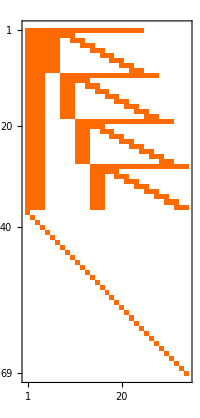

```mathematica
MatrixPlot@First@BuildHt[7,3]
```

```mathematica
ModPlus[l__]:=Mod[Plus[l],2]
```

```mathematica
Ht=First@BuildHt[7,3];
```

```mathematica
conflito=First@Select[Subsets[Ht,{4}],Plus@@ModPlus@@#==0&]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0},{1,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0}}

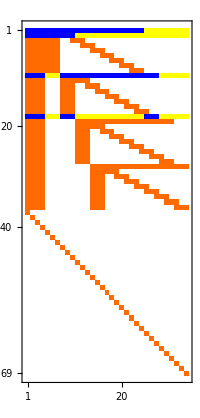

```mathematica
MatrixPlot[If[#∈conflito,#/.{0->Yellow,1->Blue},#]&/@Ht]
```